## Lab 3

Using Table and RandomInteger, generate a list of 20 random integer numbers between 20 and 50.

```mathematica
Table[RandomInteger[{20,50}], {i,20}]
```

{27,35,43,42,24,37,24,20,39,49,49,38,22,31,42,29,30,44,37,40}

Using NestList and RandomInteger, redo Question 1. Note: The first element of the list returned by NestList is not generated by RandomInteger, and it should be removed from the final answer.

```mathematica
NestList[RandomInteger[{20,50}]&,20,20 ]
```

{20,48,44,49,30,33,39,25,38,49,42,44,30,43,33,27,35,24,45,30,24}

Use Range to generate a list of the first 50 positive odd numbers. Then, use NestList to redo the question.

```mathematica
Range[1,100,2]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

Use Table and Flatten to generate a list of {x,y} where x=1/10,2/10,3/10,⋯, 6/10 and y=2/11,3/11,6/11. Then, apply Map to the list and generate a list of {x,y,x+y}.

```mathematica
Table[{x/10,y/11},{x,1,6},{y,{2,3,6}}]
```

```mathematica
{{{1/10,2/11},{1/10,3/11},{1/10,6/11}},{{1/5,2/11},{1/5,3/11},{1/5,6/11}},{{3/10,2/11},{3/10,3/11},{3/10,6/11}},{{2/5,2/11},{2/5,3/11},{2/5,6/11}},{{1/2,2/11},{1/2,3/11},{1/2,6/11}},{{3/5,2/11},{3/5,3/11},{3/5,6/11}}}
x=Flatten[%,1]
```

{{{1/10,2/11},{1/10,3/11},{1/10,6/11}},{{1/5,2/11},{1/5,3/11},{1/5,6/11}},{{3/10,2/11},{3/10,3/11},{3/10,6/11}},{{2/5,2/11},{2/5,3/11},{2/5,6/11}},{{1/2,2/11},{1/2,3/11},{1/2,6/11}},{{3/5,2/11},{3/5,3/11},{3/5,6/11}}}

{{1/10,2/11},{1/10,3/11},{1/10,6/11},{1/5,2/11},{1/5,3/11},{1/5,6/11},{3/10,2/11},{3/10,3/11},{3/10,6/11},{2/5,2/11},{2/5,3/11},{2/5,6/11},{1/2,2/11},{1/2,3/11},{1/2,6/11},{3/5,2/11},{3/5,3/11},{3/5,6/11}}

```mathematica
f[{x_,y_}]:={x,y,x+y};
Map[f,x]
```

{{1/10,2/11,31/110},{1/10,3/11,41/110},{1/10,6/11,71/110},{1/5,2/11,21/55},{1/5,3/11,26/55},{1/5,6/11,41/55},{3/10,2/11,53/110},{3/10,3/11,63/110},{3/10,6/11,93/110},{2/5,2/11,32/55},{2/5,3/11,37/55},{2/5,6/11,52/55},{1/2,2/11,15/22},{1/2,3/11,17/22},{1/2,6/11,23/22},{3/5,2/11,43/55},{3/5,3/11,48/55},{3/5,6/11,63/55}}

An integer n is a perfect square if there is an integer m such that n=m^2. Using Table, find the sum of the first 100 perfect squares.

```mathematica
Table[i^2,{i,100}]
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625,676,729,784,841,900,961,1024,1089,1156,1225,1296,1369,1444,1521,1600,1681,1764,1849,1936,2025,2116,2209,2304,2401,2500,2601,2704,2809,2916,3025,3136,3249,3364,3481,3600,3721,3844,3969,4096,4225,4356,4489,4624,4761,4900,5041,5184,5329,5476,5625,5776,5929,6084,6241,6400,6561,6724,6889,7056,7225,7396,7569,7744,7921,8100,8281,8464,8649,8836,9025,9216,9409,9604,9801,10000}

```mathematica
Total[%29]
```

338350

Refer to Question 5. Use Range to create a list of the first 5000 positive integers, then use Select to list all perfect squares which are divisible by 3. Tips: You may use a command like (Round[Sqrt[x]])^2==x to test if x is a perfect square.

```mathematica
x=Range[5000]; 
Select[x, (Mod[#,3]==0)&& Round[Sqrt[#]]^2==#&]
```

{9,36,81,144,225,324,441,576,729,900,1089,1296,1521,1764,2025,2304,2601,2916,3249,3600,3969,4356,4761}

Refer to Questions 5 and 6. Use Range to create a list of the first 5000 positive integers, then use Select to list all perfect squares which are divisible by either 3 or by 4. Note: In the condition to be applied in Select, parentheses are needed for correct order of evaluation.

```mathematica
x=Range[5000]; 
Select[x, (Mod[#,3]==0 ||Mod[#,4]==0)&& Round[Sqrt[#]]^2==#&]
```

{4,9,16,36,64,81,100,144,196,225,256,324,400,441,484,576,676,729,784,900,1024,1089,1156,1296,1444,1521,1600,1764,1936,2025,2116,2304,2500,2601,2704,2916,3136,3249,3364,3600,3844,3969,4096,4356,4624,4761,4900}

Using Table, generate e^x, e^(2x), e^(3x), ⋯, e^(5x), and then plot this group of exponential functions on a single figure over the interval [-2,3]. You may do experiment with the option PlotRange to make the graph look good.

```mathematica
Table[e^(x*i),{i,5}]
```

{e^x,e^(2 x),e^(3 x),e^(4 x),e^(5 x)}

```mathematica
Plot[Table[e^(x*i),{i,5}],{x,-2,3}]
```

-Graphics-

There are two discs with a combined circumference of 110 cm and a combined area of 550 cm^2. Find the radii of each disc.

```mathematica
Solve[{110==2*Pi*x+2*Pi*y, 550== Pi*x^2+Pi*y^2}, {x,y}]
```

{{x→(110 π-√(-12100 π^2+4400 π^3))/(4 π^2),y→(5 (11+√(11 (-11+4 π))))/(2 π)},{x→(110 π+√(-12100 π^2+4400 π^3))/(4 π^2),y→(5 (11-√(11 (-11+4 π))))/(2 π)}}

A rectangular box has a surface area of 454 cm^2. Given that one face has an area of 80 cm^2 with a perimeter of 42 cm, find the dimensions of the box.

```mathematica
Solve[{454==2*l*w+2*l*h+2*h*w, 80==l*h,42==2*l+2*h},{l,w,h}]
```

{{l→5,w→7,h→16},{l→16,w→7,h→5}}

Find a polynomial function of degree 4 that passes the points (-2,1),(0,5),(2,3),(4,2), and (5,3).

```mathematica
Clear["Global`*"]
f[x_] := a x^4+b x^3+c x^2+d x+e
Solve[{f[-2] ==1,f[0]==5,f[2]==3,f[4]==2,f[5]==3},{a,b,c,d,e}]
```

{{a→-17/1680,b→313/1680,c→-149/210,d→-103/420,e→5}}

```mathematica
f[x] /.%
```

```mathematica
{5-(103 x)/420-(149 x^2)/210+(313 x^3)/1680-(17 x^4)/1680}
%[[1]]
```

5-(103 x)/420-(149 x^2)/210+(313 x^3)/1680-(17 x^4)/1680

```mathematica
%// TraditionalForm
```

-(17 x^4)/1680+(313 x^3)/1680-(149 x^2)/210-(103 x)/420+5

The curves of f(x)=sin x^2 and g(x)=x^2-3x+2 intersect at two points. Use FindRoot to find the two points.

Sin[x^2]

2-3 x+x^2

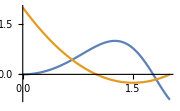

```mathematica
f[x_]= Sin[x^2]
g[x_]= x^2-3x+2
Plot[{f[x],g[x]},{x,0,2}, ImageSize-> 180]
```

```mathematica
FindRoot[Sin[x^2]==x^2-3x+2, {x,1.8}]
```

{x→1.8147}

```mathematica
{x,x^2-3x+2}/.%
```

{1.8147,-0.150964}

```mathematica
Print["The point is (", %[[1]], ", ", %[[2]], ")."]
```

The point is (1.8147, -0.150964).

```mathematica
FindRoot[Sin[x^2]==x^2-3x+2, {x,.75}]
```

```mathematica
{x->0.6717182618488124}
{x,x^2-3x+2}/.%
```

{x→0.671718}

```mathematica
{0.6717182618488124,0.4360506377547522}
Print["The point is (", %[[1]], ", ", %[[2]], ")."]
```

{0.671718,0.436051}

The point is (0.671718, 0.436051).

Plot the polynomial function 2 x^5-7 x^3-5 x^2+3x+1=0, and apply FindRoot to find each of its real roots.

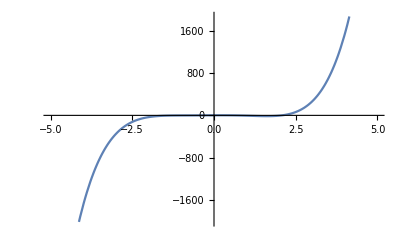

```mathematica
Plot[2 x^5-7 x^3-5 x^2+3x+1,{x,-5,5}]
```

```mathematica
FindRoot[2 x^5-7 x^3-5 x^2+3x+1==0, {x,.5}]
```

{x→0.559125}

```mathematica
FindRoot[2 x^5-7 x^3-5 x^2+3x+1==0, {x,2}]
```

{x→2.07381}

```mathematica
FindRoot[2 x^5-7 x^3-5 x^2+3x+1==0, {x,-2}]
```

{x→-0.260628}